```mathematica
pictest1=-Graphics-;
```

```mathematica
pictest1Bin=Binarize[pictest1];
```

```mathematica
pictest1Data=ImageData[pictest1Bin,DataReversed->True]//Transpose;
```

```mathematica
coords={}
```

{}

```mathematica
DynamicModule[{p={}},
EventHandler[Dynamic@Show[pictest1,Graphics[{Point[p]}],ImageSize->600],"MouseDragged":>(AppendTo[p,MousePosition["Graphics"]];coords=SortBy[IntegerPart[p],#⟦1⟧&]),"MouseDown":>(AppendTo[p,MousePosition["Graphics"]];coords=SortBy[IntegerPart[p],#⟦1⟧&])]]
```

```mathematica
pos0=Position[pictest1Data,0];
```

```mathematica
drops={#}&/@Flatten[Map[Flatten[Position[Differences[{#⟦1⟧}&/@coords]//Flatten,#]]&,{0,0}]//Union,1];
```

```mathematica
coordsRev=Delete[coords,drops];
```

```mathematica
ppp=SortBy[DeleteDuplicates[Flatten[Nearest[pos0,#]&/@coordsRev,1]],First];
```

```mathematica
ppp1=Mean/@GatherBy[ppp,#⟦1⟧&];
```

```mathematica
Show[{pictest1,ListPlot[ppp1,PlotStyle->Red]}]
```

-Graphics-

```mathematica
{{3.949224259520406,520.3554301833568}}
```

(3.94922 | 520.355)

```mathematica
LMdata={1.5/668.4062059238363*#⟦1⟧,1.5/520.3554301833568*#⟦2⟧}&/@ppp1;
```

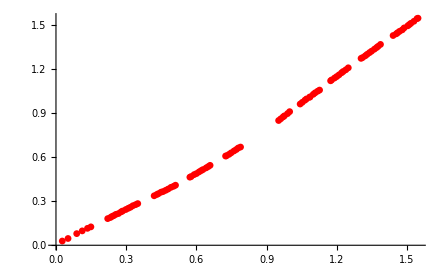

```mathematica
Show[ListPlot[Mean/@GatherBy[LMdata,Round[#⟦1⟧,0.01]&],PlotStyle->Red]]
```

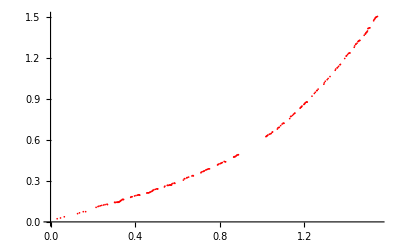

```mathematica
Show[ListPlot[LMdata,PlotStyle->{Red,PointSize[0.003]}]]
```

```mathematica
LMdata//StandardForm
```

```mathematica
LMdata={{0.020197299008229586,0.03747438552361953},{0.02244144334247732,0.03747438552361953},{0.024685587676725053,0.03747438552361953},{0.03141802067946825,0.04323967560417638},{0.03366216501371598,0.049004965684733226},{0.03590630934796371,0.051887610725011656},{0.03815045368221144,0.05477025576529008},{0.04039459801645917,0.05765290080556851},{0.04263874235070691,0.06341819088612535},{0.04712703101920237,0.0691834809666822},{0.049371175353450106,0.07783141608751748},{0.056103608356193296,0.08936199624863118},{0.060591897024688764,0.0922446412889096},{0.0628360413589365,0.10089257640974489},{0.06508018569318423,0.10377522145002331},{0.06956847436167969,0.10954051153058016},{0.07181261869592742,0.11242315657085858},{0.07405676303017515,0.11530580161113702},{0.07854505169867061,0.12107109169169386},{0.08303334036716609,0.1268363817722507},{0.08527748470141382,0.12971902681252914},{0.08976577336990928,0.135484316893086},{0.09425406203840474,0.1383669619333644},{0.09649820637265247,0.14124960697364283},{0.09874235070690021,0.14124960697364283},{0.10098649504114794,0.14413225201392127},{0.10323063937539567,0.14413225201392127},{0.10996307237813886,0.15278018713475652},{0.11220721671238659,0.1585454772153134},{0.11669550538088205,0.1614281222555918},{0.12342793838362526,0.1700760573764271},{0.125672082717873,0.17440002493684473},{0.12791622705212072,0.17872399249726237},{0.13016037138636846,0.18160663753754078},{0.13240451572061618,0.1844892825778192},{0.13464866005486392,0.19025457265837606},{0.1413810930576071,0.1960198627389329},{0.14362523739185484,0.19890250777921134},{0.15260181472884576,0.21043308794032503},{0.15709010339734122,0.2161983780208819},{0.16157839206583668,0.2277289581819956},{0.1683108250685799,0.23637689330283088},{0.17055496940282763,0.23925953834310928},{0.1772874024055708,0.24790747346394457},{0.17953154673981855,0.250790118504223},{0.18850812407680947,0.2652033437056151},{0.19748470141380042,0.2767339238667288},{0.20197299008229588,0.28249921394728567},{0.20870542308503906,0.2969124391486778},{0.21543785608778226,0.30267772922923464},{0.21768200042203,0.30556037426951305},{0.22665857775902093,0.3199735994709052},{0.23563515509601185,0.3343868246722973},{0.24685587676725051,0.34880004987368946},{0.24910002110149823,0.35168269491396786},{0.26480903144123236,0.3747438552361953},{0.2670531757754801,0.3776265002764737},{0.276029753112471,0.3891570804375874},{0.2827621861152142,0.4006876605987011},{0.2872504747837097,0.40645295067925796},{0.2917387634522052,0.41510088580009324},{0.29398290778645286,0.41798353084037165},{0.3007153407891961,0.42663146596120693},{0.31193606246043476,0.4439273362028775},{0.31866849546317794,0.4525752713237128},{0.32764507280016886,0.4669884965251049},{0.3298892171344166,0.4698711415653833},{0.34784237180839844,0.4929323018876107},{0.3657955264823803,0.5188761072501166},{0.3792603924878667,0.541937267572344},{0.39496940282760085,0.5592331378140145},{0.4084342688330872,0.5765290080556851},{0.41067841316733494,0.5794116530959634},{0.4174108461700781,0.5909422332570772},{0.4286315678413168,0.6082381034987477},{0.43087571217556453,0.6111207485390261},{0.4331198565098123,0.6140033935793046},{0.43985228951255545,0.6226513287001398},{0.4420964338468032,0.6255339737404183},{0.45331715551804186,0.6399471989418104},{0.4622937328550328,0.6543604241432025},{0.4757585988605192,0.6716562943848731},{0.48922346486600554,0.6918348096668221},{0.5094207638742352,0.7206612600696063},{0.5206414855454738,0.7350744852709984},{0.527373918548217,0.7437224203918337},{0.5341063515509602,0.7552530005529474},{0.5408387845537034,0.7639009356737827},{0.5475712175564466,0.772548870794618},{0.5498153618906944,0.7754315158348963},{0.5587919392276852,0.7869620959960101},{0.5655243722304284,0.7984926761571238},{0.5677685165646762,0.8013753211974022},{0.5722568052331717,0.8071406112779591},{0.5834775269044103,0.8215538364793512},{0.5879658155729057,0.827319126559908},{0.5991865372441444,0.8446149968015786},{0.6126514032496309,0.8619108670432492},{0.6283604135893649,0.8820893823251981},{0.6306045579236127,0.8849720273654765},{0.6328487022578604,0.887854672405755},{0.644069423929099,0.9051505426474256},{0.65304600126609,0.9137984777682608},{0.6620225786030809,0.9282117029696529},{0.6665108672715764,0.9339769930502098},{0.6732433002743196,0.942624928171045},{0.7854505169867062,1.0867571801849663},{0.7876946613209539,1.0896398252252448},{0.7899388056552017,1.0925224702655232},{0.7989153829921926,1.1011704053863585},{0.8056478159949357,1.1098183405071937},{0.8101361046634312,1.1155836305877505},{0.8123802489976789,1.118466275628029},{0.8146243933319267,1.1213489206683074},{0.8168685376661744,1.1242315657085857},{0.8191126820004222,1.1271142107488643},{0.8213568263346699,1.1299968557891427},{0.8325775480059086,1.1415274359502563},{0.8348216923401562,1.1444100809905349},{0.837065836674404,1.1472927260308132},{0.8393099810086517,1.1501753710710916},{0.8460424140113949,1.1559406611516485},{0.8482865583456427,1.1588233061919269},{0.8505307026798904,1.1617059512322054},{0.8550189913483859,1.1645885962724838},{0.8617514243511291,1.173236531393319},{0.8684838573538722,1.1818844665141544},{0.87072800168812,1.1847671115544327},{0.8752162903566154,1.1876497565947113},{0.8797045790251109,1.1905324016349896},{0.8886811563621019,1.2020629817961033},{0.8909253006963496,1.2049456268363818},{0.9043901667018359,1.2251241421183308},{0.9133667440388269,1.2366547222794444},{0.9200991770415701,1.2424200123600013},{0.9223433213758179,1.2424200123600013},{0.9268316100443132,1.2510679474808366},{0.9313198987128087,1.2568332375613933},{0.9358081873813042,1.2568332375613933},{0.9380523317155519,1.2597158826016719},{0.9470289090525429,1.2654811726822286},{0.9604937750580292,1.2683638177225072},{0.962737919392277,1.2712464627627855},{0.9739586410635157,1.2798943978836208},{0.9851793627347543,1.288542333004456},{1.0008883730744884,1.3058382032461266},{1.0076208060772316,1.308720848286405},{1.0188415277484704,1.3202514284475186},{1.0278181050854611,1.328899363568354},{1.0323063937539567,1.3317820086086325},{1.0345505380882045,1.3346646536489108},{1.0480154040936909,1.3433125887697461},{1.054747837096434,1.349077878850303},{1.0592361257649294,1.3519605238905814},{1.063724414433425,1.3577258139711383},{1.08841000211015,1.375021684212809},{1.1063631567841319,1.389434909414201},{1.1153397341211229,1.3952001994947578},{1.1265604557923614,1.4009654895753147},{1.1310487444608568,1.403848134615593},{1.1377811774636002,1.40961342469615},{1.1512460434690865,1.4182613598169853},{1.162466765140325,1.4269092949378204},{1.1759316311458115,1.4326745850183773},{1.1849082084828024,1.4384398750989342},{1.1961289301540412,1.444205165179491},{1.2006172188225366,1.4470878102197695},{1.220814517830766,1.4586183903808831},{1.2320352395020049,1.4615010354211615},{1.238767672504748,1.46438368046144},{1.2499883941759866,1.4701489705419968},{1.2544766828444822,1.4730316155822754},{1.2612091158472254,1.4759142606225537},{1.2746739818527117,1.4816795507031106},{1.281406414855455,1.484562195743389},{1.30609200253218,1.4932101308642243},{1.3173127242034186,1.4960927759045026},{1.330777590208905,1.5018580659850596},{1.339754167545896,1.504740711025338},{1.3464866005486391,1.5076233560656165},{1.35546317788563,1.5105060011058948},{1.3621956108883733,1.5133886461461732},{1.3711721882253642,1.5162712911864518},{1.3823929098966028,1.5191539362267301},{1.4048343532390801,1.533567161428122},{1.407078497573328,1.533567161428122},{1.416055074910319,1.539332451508679},{1.4182992192445665,1.539332451508679},{1.4205433635788143,1.539332451508679},{1.431764085250053,1.539332451508679},{1.4384965182527962,1.539332451508679},{1.447473095589787,1.5364498064684007},{1.4586938172610258,1.5364498064684007},{1.465426250263769,1.5364498064684007},{1.4676703945980167,1.5364498064684007},{1.4721586832665121,1.539332451508679},{1.4788911162692553,1.539332451508679},{1.481135260603503,1.539332451508679},{1.4923559822747416,1.5422150965489574},{1.4990884152774848,1.5278018713475654},{1.5013325596117326,1.5306845163878438}};
```

```mathematica
LMdata2={{0.03141802067946825,0.0230611603222274},{0.04712703101920237,0.028826450402784254},{0.06508018569318423,0.03747438552361953},{0.12791622705212072,0.06053554584584693},{0.13689280438911164,0.06630083592640378},{0.1548459590630935,0.07494877104723906},{0.16606668073433217,0.07494877104723906},{0.21543785608778226,0.10665786649030173},{0.22441443342477319,0.11242315657085858},{0.22890272209326865,0.11530580161113702},{0.23563515509601185,0.11818844665141544},{0.24236758809875505,0.12107109169169386},{0.251344165435746,0.12395373673197228},{0.2580765984384892,0.1268363817722507},{0.2670531757754801,0.12971902681252914},{0.26929732010972784,0.1268363817722507},{0.3029594851234438,0.14413225201392127},{0.3052036294576915,0.14124960697364283},{0.309691918126187,0.14413225201392127},{0.31418020679468245,0.14413225201392127},{0.3164243511289302,0.14413225201392127},{0.31866849546317794,0.14413225201392127},{0.3209126397974257,0.14413225201392127},{0.32315678413167337,0.14701489705419968},{0.3254009284659211,0.14701489705419968},{0.32764507280016886,0.14989754209447811},{0.3298892171344166,0.15278018713475652},{0.33213336146866435,0.15566283217503496},{0.33437750580291203,0.1585454772153134},{0.3388657944714075,0.16431076729587024},{0.34110993880565527,0.16431076729587024},{0.343354083139903,0.16431076729587024},{0.3455982274741507,0.16431076729587024},{0.3792603924878667,0.18016531501740157},{0.38150453682211444,0.1844892825778192},{0.38599282549060987,0.1844892825778192},{0.39721354716184853,0.19025457265837606},{0.40394598016459177,0.1931372176986545},{0.41067841316733494,0.1960198627389329},{0.41516670183583043,0.19890250777921134},{0.4174108461700781,0.19890250777921134},{0.41965499050432586,0.19890250777921134},{0.4218991348385736,0.1960198627389329},{0.4555612998522896,0.21187441046046426},{0.4578054441865373,0.21331573298060347},{0.4622937328550328,0.21331573298060347},{0.4645378771892805,0.21331573298060347},{0.46902616585777596,0.2161983780208819},{0.4712703101920237,0.2190810230611603},{0.4757585988605192,0.22196366810143875},{0.4802468875290146,0.22484631314171716},{0.48249103186326237,0.23061160322227403},{0.4847351761975101,0.23061160322227403},{0.48922346486600554,0.23637689330283088},{0.4959558978687488,0.23925953834310928},{0.502688330871492,0.24214218338338772},{0.5049324752057397,0.24214218338338772},{0.5071766195399874,0.24214218338338772},{0.5385946402194557,0.2565554085847798},{0.5408387845537034,0.2623206986653367},{0.552059506224942,0.26808598874589357},{0.5543036505591897,0.26808598874589357},{0.5587919392276852,0.26808598874589357},{0.5632802278961807,0.270968633786172},{0.5655243722304284,0.270968633786172},{0.5677685165646762,0.270968633786172},{0.5700126608989239,0.270968633786172},{0.5722568052331717,0.270968633786172},{0.5745009495674194,0.27961656890700726},{0.5789892382359149,0.28249921394728567},{0.585721671238658,0.2853818589875641},{0.5879658155729057,0.28249921394728567},{0.6283604135893649,0.3070016967896523},{0.6328487022578604,0.3170909544306268},{0.6350928465921082,0.3170909544306268},{0.644069423929099,0.3228562445111836},{0.6463135682633467,0.3257388895514621},{0.65304600126609,0.3286215345917405},{0.6687550116058241,0.33726946971257576},{0.6732433002743196,0.3401521147528542},{0.6754874446085674,0.33726946971257576},{0.711393753956531,0.36033063003480315},{0.7136378982907787,0.36609592011536},{0.7203703312935219,0.3689785651556384},{0.7248586199620174,0.37186121019591684},{0.7271027642962652,0.3747438552361953},{0.7338351972990084,0.3805091453167521},{0.7383234859675039,0.3833917903570305},{0.7428117746359992,0.386274435397309},{0.7473000633044947,0.3891570804375874},{0.7517883519729902,0.3891570804375874},{0.7899388056552017,0.41798353084037165},{0.7921829499894494,0.42086617588065006},{0.7944270943236971,0.4237488209209285},{0.8011595273264402,0.42663146596120693},{0.8056478159949357,0.42951411100148534},{0.8078919603291835,0.4323967560417638},{0.8123802489976789,0.4352794010820422},{0.8213568263346699,0.4439273362028775},{0.8258451150031654,0.44104469116259903},{0.8280892593374131,0.44104469116259903},{0.8662397130196245,0.47563643164594016},{0.8684838573538722,0.47851907668621857},{0.87072800168812,0.47851907668621857},{0.8729721460223677,0.47851907668621857},{0.8774604346908632,0.48428436676677544},{0.8797045790251109,0.48716701180705385},{0.8819487233593587,0.49004965684733226},{0.8864370120278541,0.4929323018876107},{0.8886811563621019,0.4929323018876107},{1.0188415277484704,0.6255339737404183},{1.021085672082718,0.6284166187806967},{1.0233298164169657,0.6312992638209751},{1.0255739607512135,0.6341819088612536},{1.0278181050854611,0.6370645539015319},{1.0345505380882045,0.6428298439820889},{1.0390388267567,0.6457124890223672},{1.0435271154251953,0.6485951340626457},{1.0480154040936909,0.657243069183481},{1.0502595484279384,0.6601257142237593},{1.0727009917704158,0.6812651111858011},{1.0749451361046636,0.6889521646265436},{1.079433424773159,0.6918348096668221},{1.0816775691074068,0.6947174547071004},{1.08841000211015,0.7062480348682142},{1.095142435112893,0.7177786150293278},{1.0996307237813887,0.7235439051098848},{1.1018748681156363,0.7235439051098848},{1.104119012449884,0.7235439051098848},{1.1310487444608568,0.7581356455932259},{1.1355370331293524,0.772548870794618},{1.1377811774636002,0.7754315158348963},{1.1445136104663434,0.7811968059154533},{1.1490018991348387,0.7898447410362885},{1.1534901878033341,0.7956100311168454},{1.155734332137582,0.7984926761571238},{1.180419919814307,0.8345257391606041},{1.1826640641485546,0.8388497067210218},{1.1849082084828024,0.8417323517613001},{1.1871523528170502,0.8446149968015786},{1.189396497151298,0.8503802868821354},{1.1983730744882888,0.8619108670432492},{1.2006172188225366,0.8647935120835276},{1.2028613631567844,0.8691174796439453},{1.205105507491032,0.8748827697245021},{1.2095937961595276,0.8792067372849197},{1.2118379404937751,0.8792067372849197},{1.214082084828023,0.8792067372849197},{1.2365235281705003,0.9224464128890961},{1.247744249841739,0.942624928171045},{1.2522325385102344,0.9512728632918803},{1.2589649715129776,0.9628034434529941},{1.2612091158472254,0.9656860884932724},{1.2656974045157208,0.9743340236141077},{1.2926271365266935,1.010367086617588},{1.2948712808609413,1.0204563442585626},{1.2993595695294369,1.0319869244196762},{1.3083361468664276,1.0435175045807898},{1.3128244355349232,1.0521654397016251},{1.3218010128719142,1.0665786649030173},{1.3464866005486391,1.112700985547472},{1.348730744882887,1.1213489206683074},{1.35546317788563,1.1299968557891427},{1.3577073222198779,1.132879500829421},{1.3621956108883733,1.1415274359502563},{1.3689280438911164,1.1530580161113702},{1.3711721882253642,1.1559406611516485},{1.3913694872335938,1.199180336755825},{1.398101920236337,1.2164762069974955},{1.4003460645705847,1.2193588520377738},{1.4048343532390801,1.2280067871586091},{1.4093226419075757,1.2366547222794444},{1.413810930576071,1.2395373673197227},{1.416055074910319,1.2395373673197227},{1.4362523739185484,1.28133572040376},{1.4384965182527962,1.2914249780447344},{1.4429848069212916,1.3029555582058483},{1.4452289512555394,1.3058382032461266},{1.4497172399240348,1.3116034933266836},{1.4542055285925304,1.3231340734877972},{1.456449672926778,1.3260167185280756},{1.4586938172610258,1.328899363568354},{1.4609379615952736,1.3317820086086325},{1.4631821059295211,1.3317820086086325},{1.483379404937751,1.369256394132252},{1.4878676936062463,1.3779043292530873},{1.490111837940494,1.3807869742933656},{1.4923559822747416,1.389434909414201},{1.4946001266089894,1.389434909414201},{1.4968442709432372,1.3952001994947578},{1.4990884152774848,1.4009654895753147},{1.5013325596117326,1.4182613598169853},{1.5035767039459804,1.4211440048572637},{1.5080649926144758,1.424026649897542},{1.5103091369487236,1.424026649897542},{1.5282622916227055,1.4759142606225537},{1.5305064359569531,1.484562195743389},{1.532750580291201,1.4874448407836673},{1.5349947246254487,1.4946514533843636},{1.5372388689596963,1.4989754209447812},{1.539483013293944,1.5018580659850596},{1.541727157628192,1.504740711025338},{1.5462154462966873,1.5076233560656165}};
```

## Eng p

```mathematica
pictest1=-Graphics-;
```

```mathematica
pictest1Bin=Binarize[pictest1];
```

```mathematica
pictest1Data=ImageData[pictest1Bin,DataReversed->True]//Transpose;
```

```mathematica
coords={}
```

{}

```mathematica
DynamicModule[{p={}},
EventHandler[Dynamic@Show[pictest1,Graphics[{Point[p]}],ImageSize->600],"MouseDragged":>(AppendTo[p,MousePosition["Graphics"]];coords=SortBy[IntegerPart[p],#⟦1⟧&]),"MouseDown":>(AppendTo[p,MousePosition["Graphics"]];coords=SortBy[IntegerPart[p],#⟦1⟧&])]]
```

```mathematica
pos0=Position[pictest1Data,0];
```

```mathematica
drops={#}&/@Flatten[Map[Flatten[Position[Differences[{#⟦1⟧}&/@coords]//Flatten,#]]&,{0,0}]//Union,1];
```

```mathematica
coordsRev=Delete[coords,drops];
```

```mathematica
ppp=SortBy[DeleteDuplicates[Flatten[Nearest[pos0,#]&/@coordsRev,1]],First];
```

```mathematica
ppp1=Mean/@GatherBy[ppp,#⟦1⟧&];
```

```mathematica
Show[{pictest1,ListPlot[ppp1,PlotStyle->Red]}]
```

-Graphics-

```mathematica
{{"13.85","23.46"}}
```

```mathematica
{{"7.692","513.5"}}
```

```mathematica
{{3.949224259520406,520.3554301833568}}
```

(3.94922 | 520.355)

```mathematica
LMEpdata={1.5/666.2*#⟦1⟧,15/(513.5-23.46)*(#⟦2⟧-23.46)}&/@ppp1;
```

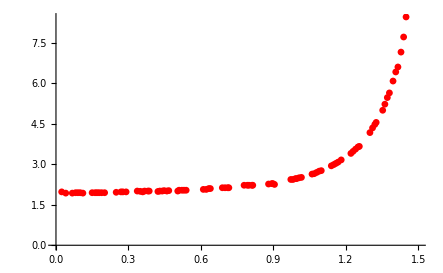

```mathematica
Show[ListPlot[Mean/@GatherBy[LMEpdata,Round[#⟦1⟧,0.01]&],PlotStyle->Red]]
```

```mathematica
LMEpdata//StandardForm
```

{{0.0225158,1.97555},{0.0247673,1.97555},{0.0382768,1.94494},{0.0427799,1.91433},{0.0652957,1.91433},{0.0697989,1.94494},{0.0788052,1.94494},{0.0833083,1.94494},{0.0855599,1.94494},{0.0923146,1.94494},{0.0945662,1.94494},{0.0968178,1.94494},{0.101321,1.94494},{0.103573,1.94494},{0.110327,1.94494},{0.112579,1.91433},{0.146352,1.94494},{0.153107,1.94494},{0.162113,1.94494},{0.166617,1.94494},{0.173371,1.94494},{0.175623,1.94494},{0.177875,1.94494},{0.182378,1.94494},{0.189132,1.94494},{0.198139,1.94494},{0.204893,1.94494},{0.245422,1.94494},{0.247673,1.94494},{0.249925,1.97555},{0.254428,1.97555},{0.265686,1.97555},{0.267938,1.97555},{0.270189,1.97555},{0.272441,1.97555},{0.276944,1.97555},{0.288202,2.00616},{0.290453,1.97555},{0.292705,1.94494},{0.335485,2.00616},{0.337736,2.00616},{0.346743,2.00616},{0.348994,2.00616},{0.351246,1.97555},{0.355749,1.97555},{0.358001,1.97555},{0.360252,1.97555},{0.362504,1.97555},{0.367007,2.00616},{0.380516,2.00616},{0.38502,2.00616},{0.387271,2.00616},{0.421045,1.97555},{0.423296,2.00616},{0.425548,2.00616},{0.430051,2.00616},{0.434554,2.00616},{0.439057,2.00616},{0.441309,2.00616},{0.445812,2.03677},{0.450315,2.00616},{0.459322,2.00616},{0.466076,2.03677},{0.468328,2.00616},{0.504353,2.00616},{0.508856,2.03677},{0.511108,2.03677},{0.517863,2.03677},{0.522366,2.03677},{0.524617,2.03677},{0.526869,2.03677},{0.52912,2.03677},{0.531372,2.03677},{0.533624,2.03677},{0.535875,2.03677},{0.538127,2.03677},{0.540378,2.03677},{0.54263,2.03677},{0.610177,2.06738},{0.621435,2.06738},{0.623687,2.06738},{0.632693,2.09799},{0.639448,2.09799},{0.688982,2.1286},{0.70024,2.1286},{0.711498,2.1286},{0.716001,2.1286},{0.779045,2.22043},{0.792555,2.22043},{0.79931,2.22043},{0.810567,2.22043},{0.812819,2.22043},{0.815071,2.22043},{0.875863,2.25104},{0.884869,2.28165},{0.893876,2.28165},{0.898379,2.28165},{0.905134,2.25104},{0.970429,2.4347},{0.974932,2.4347},{0.981687,2.4347},{0.990693,2.46531},{0.992945,2.46531},{0.995197,2.46531},{0.997448,2.46531},{1.00645,2.49592},{1.01546,2.52653},{1.01771,2.49592},{1.05824,2.61836},{1.06274,2.64897},{1.0695,2.64897},{1.07625,2.67958},{1.08301,2.71019},{1.08976,2.7408},{1.09652,2.77141},{1.09877,2.77141},{1.10102,2.7408},{1.13705,2.92446},{1.1438,2.95506},{1.15056,2.98567},{1.15731,3.01628},{1.16181,3.04689},{1.16857,3.0775},{1.17757,3.13872},{1.18208,3.16933},{1.18433,3.16933},{1.22035,3.3836},{1.22261,3.41421},{1.22711,3.44482},{1.22936,3.47543},{1.23161,3.47543},{1.23386,3.50604},{1.23837,3.53665},{1.24062,3.56726},{1.24287,3.56726},{1.24737,3.59787},{1.24962,3.62848},{1.25188,3.65909},{1.25413,3.65909},{1.25638,3.65909},{1.29916,4.12844},{1.30141,4.21006},{1.30591,4.27128},{1.31267,4.36311},{1.31492,4.39372},{1.31717,4.42433},{1.31942,4.45494},{1.32168,4.48555},{1.32393,4.51616},{1.32618,4.54677},{1.3532,4.99571},{1.35995,5.18958},{1.36446,5.2508},{1.37121,5.43445},{1.37346,5.49567},{1.37796,5.5875},{1.38022,5.64872},{1.38472,5.67933},{1.39598,6.07726},{1.40724,6.41397},{1.41624,6.59762},{1.42525,6.99555},{1.42975,7.1486},{1.432,7.30165},{1.43651,7.48531},{1.43876,7.63836},{1.44101,7.73019},{1.44326,7.97506},{1.45002,8.44951},{1.45677,8.92397},{1.46127,9.19945},{1.46578,9.50555},{1.46803,10.0259},{1.47028,10.1484},{1.47253,10.3626},{1.47478,10.5769},{1.47929,10.9136},{1.48154,11.1279},{1.48379,11.4646},{1.48604,11.587},{1.49054,12.4135},{1.49279,12.9032},{1.49505,13.1175},{1.49955,15.2602},{1.50405,14.546}}

```mathematica
θ211=Import["D:\\Dropbox\\PDF Euclidean Lattice\\Large Nc 2 dim QCD\\C\\FIE\\FIE\\data.dat"];
```

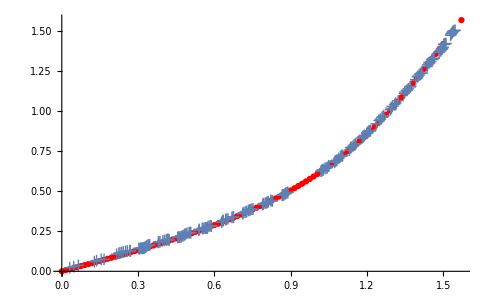

```mathematica
Show[{ListPlot[θ211,PlotStyle->Red],ListPlot[LMdata2,PlotMarkers->Style["+",12]]}]
```